```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=Flatten @ Import["test2-std.dat"];
```

```mathematica
len=Length[l]
1./Sqrt[len]
```

65536

0.00390625

```mathematica
Mean[l]
StandardDeviation[l]
```

7.06656×10^-10

1.00001

{1.,0.755797,0.639275,0.584379,0.541111,0.507724,0.478311,0.456251,0.436903,0.419375,0.403291,0.388961,0.377223,0.366032,0.353774,0.345524,0.335393,0.327222,0.319066,0.312944,0.307017}

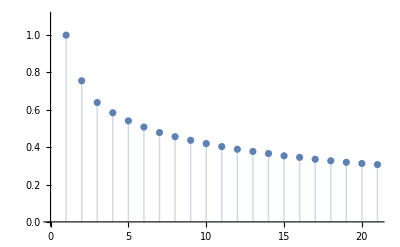

9.65557

```mathematica
cf=CorrelationFunction[l,{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```

```mathematica
(* Allan variance estimate *)
diffs=Most[l]-Rest[l];
sqdiffs=diffs^2;
sumsqdiffs=Total[sqdiffs];
avar=sumsqdiffs/(2len)
adev=Sqrt[avar]
```

0.244199

0.494165

```mathematica
(* Convert to integers *)
lint=N@Round[l];
Mean[lint]
StandardDeviation[lint]
```

0.000396729

1.04057

```mathematica
(* Allan variance estimate *)
diffs=Most[lint]-Rest[lint];
sqdiffs=diffs^2;
sumsqdiffs=Total[sqdiffs];
avar=sumsqdiffs/(2len)
adev=Sqrt[avar]
```

0.327477

0.572256

{1.,0.697548,0.591728,0.539247,0.500296,0.470716,0.440375,0.421026,0.404101,0.386612,0.372083,0.357793,0.346857,0.335358,0.324845,0.316305,0.3083,0.300113,0.292277,0.290487,0.282948}

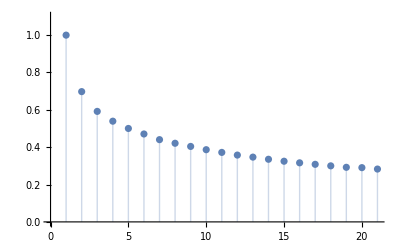

8.97901

```mathematica
cf=CorrelationFunction[N[lint],{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```

0.

{a→24787.7,x0→-0.00618317,σ→1.06063}

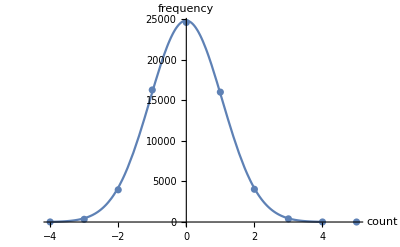

```mathematica
(* Distribution *)
ta=Tally[lint];
x0est=Sort[ta,#1[[2]]>#2[[2]]&][[1,1]]
p1=ListPlot[ta,AxesLabel->{"count","frequency"},LabelStyle->Larger];
fnc=a Exp[-(x-x0)^2/(2σ^2)];
sol=FindFit[ta,fnc,{{a,20000},{x0,x0est},{σ,1}},x]
fnc=fnc/.sol;
p2=Plot[fnc,{x,-4,4},PlotRange->All];
pp=Show[p1,p2]
```

0.999542

{1.,0.0646588,0.0235179,0.0117628,0.00950284,0.0108275,0.00691356,0.0127609,0.0085085,0.00349977,0.00194982,0.00720277,-0.000935124,0.00750899,0.00306439,0.00509661,-0.00397619,0.00745289,0.00665119,0.00417798,0.00490001}

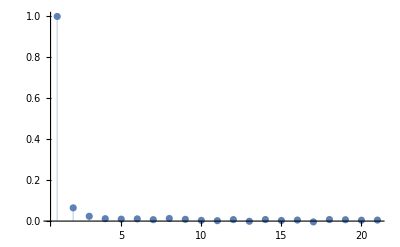

1.19505

```mathematica
(* LSB correlations *)
l2=Map[Mod[#,2]&,l];
Mean[l2]
cf=CorrelationFunction[l2,{20}]
ListPlot[cf,Filling->0,PlotRange->All]
Total[cf]
```